```mathematica
SetDirectory[NotebookDirectory[]<>"simulation_data/"]
```

/Users/chaitanyagokhale/Documents/Working/Srishti/Overleafdata/matecopying_multiplemorphs/fig3_new/simulation_data

```mathematica
filenames=FileNames[];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/chaitanyagokhale/Documents/Working/Srishti/Overleafdata/matecopying_multiplemorphs/fig3_new

```mathematica
raw3mdata=Table[Import[NotebookDirectory[]<>"simulation_data/"<>ToString[filenames⟦i⟧],"CSV"],{i,1,Length[filenames],1}];
```

```mathematica
raw3mdata//Dimensions
```

{20,1275,3}

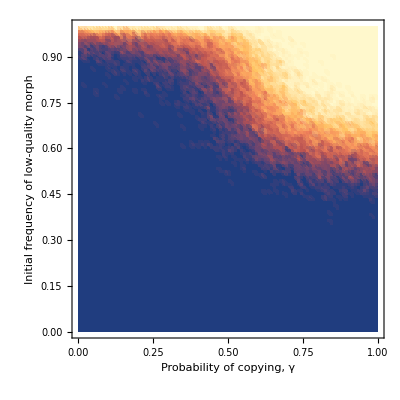

```mathematica
ListDensityPlot[rawfig2a⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}]
```

```mathematica
rawfig2b=Import[NotebookDirectory[]<>"fig2b_data.csv","CSV"];
```

```mathematica
rawfig2b⟦2;;10⟧
```

{{0.,0.,0.},{0.,0.01,0.0005},{0.,0.02,0.004},{0.,0.03,0.006},{0.,0.04,0.0075},{0.,0.05,0.0085},{0.,0.06,0.0095},{0.,0.07,0.0105},{0.,0.08,0.011}}

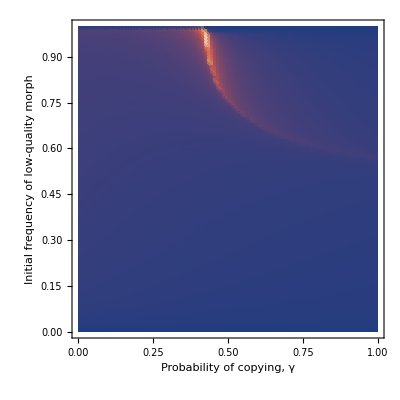

```mathematica
ListDensityPlot[rawfig2b⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Normalised fixation time",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}]
```

```mathematica
rawfig2c=Import[NotebookDirectory[]<>"fig2c_data.csv","CSV"];
```

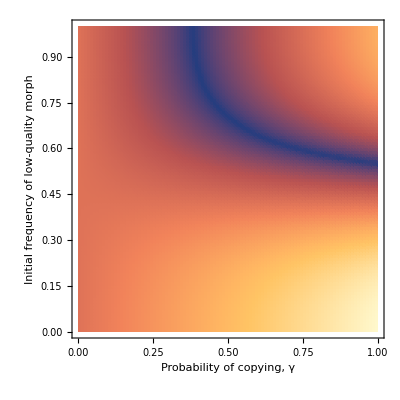

```mathematica
ListDensityPlot[rawfig2c⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Absolute difference in modified qualities",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}]
```